## Perform AUC calculations for a normal distribution

```mathematica
fx[x_]:=1/(√(2π))Exp[-1/2(x)^2];
fnormal[x_,mu_,sigma_]:=1/sigma*fx[(x-mu)/sigma];
```

#### The step-size: magnitude between two consecutive data points on the x-axis

```mathematica
step=0.1;
```

### Create export function

```mathematica
plotexporter[plotObject_,path_]:=Export[path,plotObject];
```

### Create average calculator

```mathematica
average[data_]:=1/Length[data]*Sum[data[[i]],{i,1,Length[data]}];
```

### Create the normal distribution based on the normal function “fnormal”

```mathematica
normalTuple[x_,mu_,sigma_]:={x,fnormal[x,mu,sigma]};
distribution[mu_,sigma_,delta_]:=Table[normalTuple[arg,mu,sigma],{arg,-delta,delta,0.1}];
fdist[mu_,sigma_,delta_]:=Table[fnormal[arg,mu,sigma],{arg,-delta,delta,step}];
```

### Calculate the average delta between the x-arguments

```mathematica
dx[params_]:=Table[distribution[params[[1]],params[[2]],params[[3]]][[n]][[2]]-distribution[params[[1]],params[[2]],params[[3]]][[n-1]][[2]],{n,2,Length[distribution[params[[1]],params[[2]],params[[3]]]]}];
avgdx[params_]:=average[dx[params[[1]],params[[2]],params[[3]]]];
```

### Create a graphical representation of the normal distribution Set a group of testing parameters: mean μ, standard deviation σ, the “spread” of the distribution δ

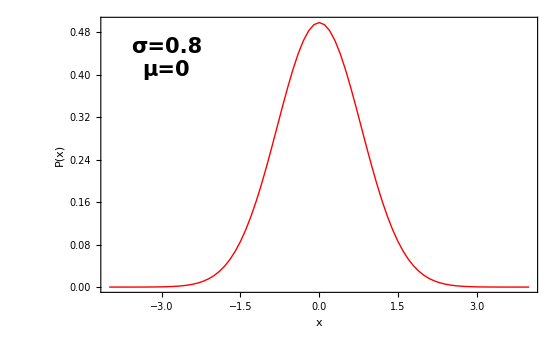

```mathematica
testParams={0,0.8,4};
distPlotter[params_]:=ListPlot[distribution[params[[1]],params[[2]],params[[3]]],Joined->True,PlotRange->All,Frame->True,Axes->False,PlotStyle->{Red,Thick},LabelStyle->{18,Bold,Black,FontFamily->"Times"},FrameLabel->{"x","P(x)"},FrameStyle->Directive[Black,Thick],ImageSize->{560.,420.},Epilog->Inset[Style[StringTemplate["σ=``\nμ=``"][params[[2]],params[[1]]],Bold,Black,21,FontFamily->"Times"],Scaled[{0.15,0.85}]]];
Show[distPlotter[testParams]]
```

### Create the AUC components of the algorithm (normal distribution)

If the x-value is less than the right limit (for left-side auc) and higher than the left limit (for right-side auc), the condition for valid term within the summation is passed

```mathematica
condLeft[x_,rightLimit_]:=If[x<=rightLimit,x,0];
condRight[x_,leftLimit_]:=If[x<=leftLimit,x,0];
```

```mathematica
distTable[params_]:=Table[fnormal[i,params[[1]],params[[2]]],{i,-params[[3]],params[[3]],step}];
aucLeft[params_,rightLimit_]:=Sum[condLeft[distTable[params][[i]],rightLimit],{i,1,Length[distTable[params]]}];
```

```mathematica
distTable[testParams]
aucLeft[testParams,2]
```

{1.8584×10^-6,3.44493×10^-6,6.28688×10^-6,0.0000112955,0.0000199797,0.0000347925,0.0000596483,0.000100676,0.000167288,0.000273665,0.000440745,0.000698827,0.00109085,0.0016764,0.00253631,0.00377782,0.00553981,0.00799765,0.011367,0.0159052,0.0219104,0.0297149,0.0396746,0.0521512,0.0674887,0.0859828,0.107847,0.133173,0.161897,0.193765,0.228311,0.264846,0.302463,0.340069,0.376422,0.410201,0.440082,0.464819,0.483335,0.494797,0.498678,0.494797,0.483335,0.464819,0.440082,0.410201,0.376422,0.340069,0.302463,0.264846,0.228311,0.193765,0.161897,0.133173,0.107847,0.0859828,0.0674887,0.0521512,0.0396746,0.0297149,0.0219104,0.0159052,0.011367,0.00799765,0.00553981,0.00377782,0.00253631,0.0016764,0.00109085,0.000698827,0.000440745,0.000273665,0.000167288,0.000100676,0.0000596483,0.0000347925,0.0000199797,0.0000112955,6.28688×10^-6,3.44493×10^-6,1.8584×10^-6}

10.

### Calculate the average spacings (in terms of their numerical values) of the normal distribution

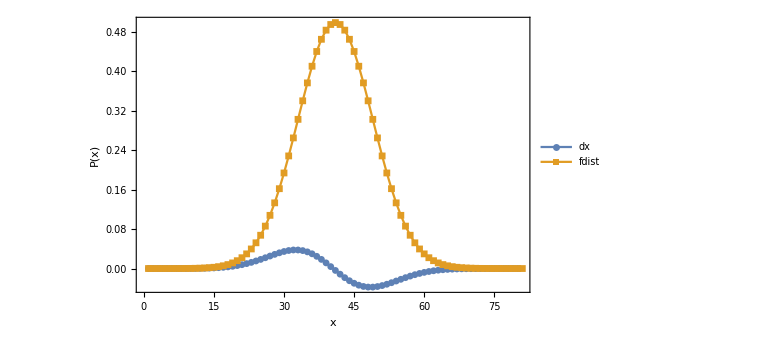

μ_dx=1.6

```mathematica
ListPlot[{dx[testParams],fdist[testParams[[1]],testParams[[2]],testParams[[3]]]},PlotRange->Full,ImageSize->{560.,420.},Joined->True,PlotMarkers->{Automatic, Small},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotLegends->Placed[{"dx","fdist"},{0.2,0.8}],FrameLabel->{"x","P(x)"},LabelStyle->{18,Bold,Black,FontFamily->"Times"}]
Print[Style[StringTemplate["μ_dx=``"][avgdx[testParams]],20,Red,Bold,FontFamily->"Times"]]
```